Import experimental data

```mathematica
Needs["ErrorBarPlots`"]
```

This assumes that the experimental data are saved in the same folder as the mathematica file
Geometrical informations
Order of data: 1- dev_stage, 2 - cell volume, 3 - Number of cells N, 4- Tissue Volume V, 5- N/V, 6- Nucleus_major, 7- Nucleus_minor, 8-h, 9- A_apical, 10- A_basal, 11-aspectratio_cell, 12 aspectratio_tissue

```mathematica
data=Import[StringJoin[NotebookDirectory[],"data_F1_corr.csv"]];
dataGeom=Table[ToExpression[StringSplit[data[[k]],";"][[1]]],{k,2,7}];
stdGeom=Table[ToExpression[StringSplit[data[[k]],";"][[1]]],{k,9,14}];
dataGeom//TableForm
stdGeom//TableForm
```

20 | 438.051 | 2177.3 | 903507. | 0.00240983 | NA | NA | 42.3486 | 51116. | 12625.9 | 0.238566 | 11.4719 | 31870.9
24 | 267.873 | 3039.6 | 995010. | 0.00305484 | 13.0836 | 4.30317 | 39.1638 | 52083.1 | 15755.7 | 0.213179 | 11.8322 | 33919.4
30 | 252.97 | 5909.1 | 1353373 | 0.0043662 | 13.2653 | 4.33094 | 45.011 | 66690.1 | 15178.6 | 0.222905 | 17.564 | 40934.3
36 | 222.651 | 6664.4 | 1712359 | 0.00389194 | 13.0433 | 4.0907 | 46.436 | 78844.4 | 18119.8 | 0.21283 | 17.6544 | 48482.1
42 | 167.5 | 15509.5 | 3025227 | 0.00512672 | 11.2436 | 3.88541 | 63.2462 | 107606. | 23241.3 | 0.247812 | 32.763 | 65423.5
48 | 144.597 | 17955 | 3981915 | 0.00450914 | 11.6757 | 3.87359 | 63.8642 | 128755. | 31674.9 | 0.225605 | 31.3984 | 80214.9

20 | 60.3609 | 708.426 | 147164. | 0.000681987 | NA | NA | 3.97862 | 5259.7 | 6635.49 | 0.0273711 | 2.21542 | 4037.76
24 | 33.6717 | 555.574 | 242652. | 0.000575684 | 1.1601 | 0.620223 | 5.28899 | 8543.31 | 1939.3 | 0.0226958 | 1.56418 | 4875.86
30 | 40.926 | 924.317 | 122050. | 0.000363642 | 1.37048 | 0.385122 | 1.77294 | 5191.91 | 2885. | 0.011782 | 1.29695 | 3239.47
36 | 37.1423 | 2095.62 | 435317. | 0.000645038 | 1.26711 | 0.445937 | 3.64491 | 16436.8 | 3903.83 | 0.0216902 | 2.24364 | 8563.54
42 | 22.5547 | 1117.09 | 370756. | 0.000641157 | 1.26537 | 0.488755 | 6.08553 | 9164.39 | 5712.76 | 0.0249379 | 2.27473 | 6262.01
48 | 38.0784 | 2656.06 | 525919. | 0.000445574 | 0.865023 | 0.392442 | 4.53671 | 12318.4 | 3758.84 | 0.01195 | 3.19558 | 6432.82

Load ratio of apical and basal surface areas

```mathematica
data=Import[StringJoin[NotebookDirectory[],"TccCurvature_err.csv"]];
dataForratioAaAb=Table[ToExpression[StringSplit[data[[k]],";"][[1]]],{k,2,7}];
```

Number of neurons
Order of data: 1- dev_stage, 2 Number of cells N, 3- V/v, 4-Number of neurons

```mathematica
data=Import[StringJoin[NotebookDirectory[],"data_F1-S.csv"]];
dataDiff=Table[ToExpression[StringSplit[data[[k]],";"][[1]]],{k,2,7}];
stdDiff=Table[ToExpression[StringSplit[data[[k]],";"][[1]]],{k,9,14}];
dataDiff//TableForm
stdDiff//TableForm
```

20 | 2177.3 | 2163.4 | NaN
24 | 3039.6 | 3721.7 | NaN
30 | 5909.1 | 5456.82 | NaN
36 | 6664.4 | 8028.06 | 1046
42 | 15509.5 | 18130.7 | 3319
48 | 17955 | 29627.2 | 9462

20 | 708.426 | 1185.42 | NaN
24 | 555.574 | 875.602 | NaN
30 | 924.317 | 1028.3 | NaN
36 | 2095.62 | 2933.46 | NaN
42 | 1117.09 | 2276.13 | NaN
48 | 2656.06 | 10715.8 | NaN

Cell cycle lengths: all data
Order of data: 1- Tcc in hours, 2-stage, 3-binning

```mathematica
data=Import[StringJoin[NotebookDirectory[],"data_F2_CellCycle.csv"]];
dataCellCycle=Table[ToExpression[StringSplit[data[[k]],";"][[1]]],{k,2,271}];
```

Cell cycle length, binned
Order of data: 1- dev_stag
e, 2-Mitotic_index, 3-Tcc in hours, 4-Tcc_Coeffvariation

```mathematica
data=Import[StringJoin[NotebookDirectory[],"data_F2.csv"]];
dataCellCycleBinned=Table[ToExpression[StringSplit[data[[k]],";"][[1]]],{k,2,7}];
dataCellCycleBinnedStd=Table[{dataCellCycleBinned[[i,4]]*dataCellCycleBinned[[i,3]]},{i,1,6}];
dataCellCycleBinned//TableForm
dataCellCycleBinnedStd//TableForm
```

20 | 0.0253818 | NaN | NaN
24 | 0.0220432 | 5.96875 | 0.34433
30 | 0.0274188 | 7.3506 | 0.437755
36 | 0.0438798 | 5.68778 | 0.310263
42 | 0.0415799 | 5.33559 | 0.209546
48 | 0.0328493 | 6.6 | 0.283764

NaN^2
2.05522
3.21776
1.76471
1.11805
1.87284

Load data into arrays

```mathematica
datav=Table[{dataGeom[[i,1]],dataGeom[[i,2]]},{i,1,6}]; (*cell volume*)
datastdv=Table[{stdGeom[[i,1]],stdGeom[[i,2]]},{i,1,6}];

dataNt=Table[{dataGeom[[i,1]],dataGeom[[i,3]]},{i,1,6}]; (*Number of cells*)
datastdNt=Table[{stdGeom[[i,1]],stdGeom[[i,3]]},{i,1,6}];

datah=Table[{dataGeom[[i,1]],dataGeom[[i,8]]},{i,1,6}]; (*Tissue height*)
datastdh=Table[{stdGeom[[i,1]],stdGeom[[i,8]]},{i,1,6}];

dataV=Table[{dataGeom[[i,1]],dataGeom[[i,4]]},{i,1,6}]; (*Tissue volume*)
datastdV=Table[{stdGeom[[i,1]],stdGeom[[i,4]]},{i,1,6}];

dataAa=Table[{dataGeom[[i,1]],dataGeom[[i,9]]},{i,1,6}]; (*Apical area*)
datastdAa=Table[{stdGeom[[i,1]],stdGeom[[i,9]]},{i,1,6}];

dataAb=Table[{dataGeom[[i,1]],dataGeom[[i,10]]},{i,1,6}];
datastdAb=Table[{stdGeom[[i,1]],stdGeom[[i,10]]},{i,1,6}]; (*Basal area*)

dataAa=Table[{dataGeom[[i,1]],dataGeom[[i,9]]},{i,1,6}]; (*Apical area*)
datastdAa=Table[{stdGeom[[i,1]],stdGeom[[i,9]]},{i,1,6}];

dataAm=Table[{dataGeom[[i,1]],dataGeom[[i,13]]},{i,1,6}]; (*average of apical and basal area*)
datastdAm=Table[{stdGeom[[i,1]],stdGeom[[i,13]]},{i,1,6}];

dataratioAaAb=Table[{dataForratioAaAb[[i,1]],dataForratioAaAb[[i,4]]},{i,1,6}] ; (*ratio of apical to basal surface area*)
datastdratioAaAb=Table[{dataForratioAaAb[[i,1]],dataForratioAaAb[[i,5]]},{i,1,6}] ;

dataNn=Table[{dataDiff[[i,1]],dataDiff[[i,4]]},{i,1,6}]; (*Number of neurons*)
datastdNn=Table[{stdDiff[[i,1]],stdDiff[[i,4]]},{i,1,6}];

(*the NaNs for the number of neurons at 20-30 hours correspond in fact to 0 neurons*)
dataNn[[1,2]]=0;
dataNn[[2,2]]=0;
dataNn[[3,2]]=0;


(*show data*)
Print["total number of cells, average "]
dataNt//TableForm
Print["total number of cells, std "]
datastdNt//TableForm

Print["number of neurons, average "]
dataNn//TableForm
Print["number of neurons, std "]
datastdNn//TableForm

Print["Total tissue volume, average"]
dataV//TableForm
Print["Total tissue volume, std"]
datastdV//TableForm

Print["Cell volume, average"]
datav//TableForm
Print["Cell volume, std"]
datastdv//TableForm

Print["tissue height, average"]
datah//TableForm
Print["tissue height, std"]
datastdh//TableForm

Print["Apical area, average"]
dataAa//TableForm
Print["Apical area, std"]
datastdAa//TableForm

Print["Basal area, average"]
dataAb//TableForm
Print["Basal area, std"]
datastdAb//TableForm


Print["Apical and Basal area average, average"]
dataAm//TableForm
Print["Apical and Basal area average, std"]
datastdAm//TableForm

Print["Ratio of Apical to Basal area, average"]
dataratioAaAb//TableForm

Print["Ratio of Apical to Basal area, std"]
datastdratioAaAb//TableForm
```

total number of cells, average

20 | 2177.3
24 | 3039.6
30 | 5909.1
36 | 6664.4
42 | 15509.5
48 | 17955

total number of cells, std

20 | 708.426
24 | 555.574
30 | 924.317
36 | 2095.62
42 | 1117.09
48 | 2656.06

number of neurons, average

20 | 0
24 | 0
30 | 0
36 | 1046
42 | 3319
48 | 9462

number of neurons, std

20 | NaN
24 | NaN
30 | NaN
36 | NaN
42 | NaN
48 | NaN

Total tissue volume, average

20 | 903507.
24 | 995010.
30 | 1353373
36 | 1712359
42 | 3025227
48 | 3981915

Total tissue volume, std

20 | 147164.
24 | 242652.
30 | 122050.
36 | 435317.
42 | 370756.
48 | 525919.

Cell volume, average

20 | 438.051
24 | 267.873
30 | 252.97
36 | 222.651
42 | 167.5
48 | 144.597

Cell volume, std

20 | 60.3609
24 | 33.6717
30 | 40.926
36 | 37.1423
42 | 22.5547
48 | 38.0784

tissue height, average

20 | 42.3486
24 | 39.1638
30 | 45.011
36 | 46.436
42 | 63.2462
48 | 63.8642

tissue height, std

20 | 3.97862
24 | 5.28899
30 | 1.77294
36 | 3.64491
42 | 6.08553
48 | 4.53671

Apical area, average

20 | 51116.
24 | 52083.1
30 | 66690.1
36 | 78844.4
42 | 107606.
48 | 128755.

Apical area, std

20 | 5259.7
24 | 8543.31
30 | 5191.91
36 | 16436.8
42 | 9164.39
48 | 12318.4

Basal area, average

20 | 12625.9
24 | 15755.7
30 | 15178.6
36 | 18119.8
42 | 23241.3
48 | 31674.9

Basal area, std

20 | 6635.49
24 | 1939.3
30 | 2885.
36 | 3903.83
42 | 5712.76
48 | 3758.84

Apical and Basal area average, average

20 | 31870.9
24 | 33919.4
30 | 40934.3
36 | 48482.1
42 | 65423.5
48 | 80214.9

Apical and Basal area average, std

20 | 4037.76
24 | 4875.86
30 | 3239.47
36 | 8563.54
42 | 6262.01
48 | 6432.82

Ratio of Apical to Basal area, average

20 | 4.97538
24 | 3.31313
30 | 4.54165
36 | 4.52063
42 | 4.84296
48 | 4.115

Ratio of Apical to Basal area, std

20 | 2.10378
24 | 0.462266
30 | 0.949206
36 | 1.36944
42 | 1.09884
48 | 0.617152

Graph of cell cycle time - binned.

Mean cell cycle length and rate of cell division

```mathematica
Tccmean=Mean[Table[dataCellCycle[[i,1]],{i,1,Length[dataCellCycle]}]]
kd=Log[2]/Tccmean
```

6.20981

0.111621

Plot showing binned cell cycle time - for Fig. S4C

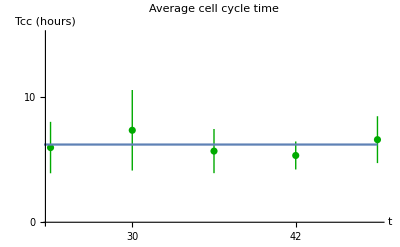

```mathematica
Show[ErrorListPlot[Table[{{dataCellCycleBinned[[i,1]],dataCellCycleBinned[[i,3]]},ErrorBar[dataCellCycleBinnedStd[[i,1]]]},{i,2,6}],PlotRange->{0,15},PlotLabel->"Average cell cycle time",PlotStyle->{Thick,Darker[Green]},AxesStyle->Thick,LabelStyle->{FontSize->16,FontFamily->"Helvetica",Black},AxesLabel->{t,"Tcc (hours)"},Ticks->{{20,24,30,36,42,48},{0,10,20}}],Plot[Tccmean,{t,20,48}]]
```

Plot ratio of apical to basal area - for Fig. S4C
The average ratio of apical to basal area, sexp, is determined from experimental measurements.

4.38479

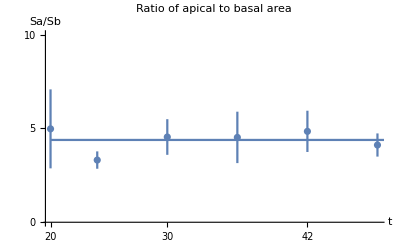

```mathematica
sexp=Mean[Table[dataratioAaAb[[i,2]],{i,1,6}]]
Show[ErrorListPlot[Table[{{dataAa[[i,1]],dataratioAaAb[[i,2]]},ErrorBar[datastdratioAaAb[[i,2]]]},{i,1,6}],PlotRange->{0,10}],Plot[sexp,{t,20,50}],PlotLabel->"Ratio of apical to basal area",PlotStyle->{Thick,Darker[Green]},AxesStyle->Thick,LabelStyle->{FontSize->16,FontFamily->"Helvetica",Black},AxesLabel->{t,Sa/Sb},Ticks->{{20,24,30,36,42,48},{0,5,10}}]
```

Solve for the number of cells and adjust for differentiation probability

Fit with a two step process and all divisions being symmetric (α=1)
pfunc allows to vary the fraction of cells that differentiate as a function of time
Follow Eqs. 1-3

```mathematica
pfunc[t_,p_]=Piecewise[{{1,t≤35},{p,t>35}}];
sol[k_,p_?NumericQ,α_?NumericQ,N0_?NumericQ]:=NDSolve[{Np'[t]==k(pfunc[t,p]+α  pfunc[t,p]-α)Np[t],Nn'[t]==k(1- pfunc[t,p])(1+α) Np[t],Nt'[t]==k Np[t],Nt[20]== N0,Nn[20]==0,Np[20]==N0},{Np[t],Nt[t],Nn[t]},{t,20,48}]
ObjectiveFunction[p_?NumericQ,α_?NumericQ,N0_?NumericQ]:=Module[{s,Ntsol,Nnsol},s:=sol[kd,p,α,N0];Ntsol[t_]:=Nt[t]/.s;Nnsol[t_]:=Nn[t]/.s;Sum[((Ntsol[t]/.{t->dataNt[[j,1]]})-dataNt[[j,2]])^2/((Mean[Table[dataNt[[j,2]],{j,1,6}]])^2)+((Nnsol[t]/.{t->dataNn[[j,1]]})-dataNn[[j,2]])^2/((Mean[Table[dataNn[[j,2]],{j,1,6}]])^2),{j,1,6}]][[1]]
```

```mathematica
FindMinimum[ObjectiveFunction[p,1,N0],{{p,0.8},{N0,2000}},Method->"PrincipalAxis"]
```

{0.497624,{p→0.652631,N0→1321.57}}

Save the result for later

```mathematica
N0fit=1321.57
p0fit=0.652
```

1321.57

0.652

Fit to the tissue volume

Fit logarithm of volume

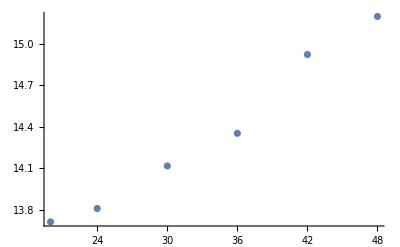

12.5105+0.0552646 x

```mathematica
datalnV=Table[{dataV[[i,1]],Log[dataV[[i,2]]]},{i,1,6}];
ListPlot[datalnV]
Fit[datalnV,{1,x},x]
```

Result for volume rate of growth

```mathematica
g=0.0552646;
```

Initial volume obtained from the fit

```mathematica
V0fit=Exp[12.51] Exp[g  20]
```

818552.

Volume doubling time

```mathematica
Log[2]/g
```

12.5423

Plot the resulting fitted curve for tissue volume, together with experimental data

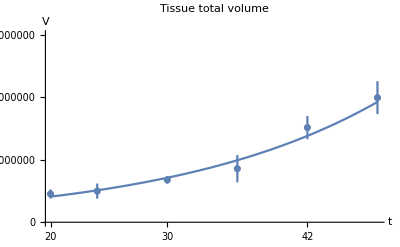

```mathematica
Show[ErrorListPlot[Table[{{dataV[[i,1]],dataV[[i,2]]},ErrorBar[datastdV[[i,2]]]},{i,1,6}],PlotRange->{0,6*10^6}],Plot[V0fit Exp[g ( t-20)],{t,20,48}],PlotLabel->"Tissue total volume",PlotStyle->{Thick,Darker[Green]},AxesStyle->Thick,LabelStyle->{FontSize->16,FontFamily->"Helvetica",Black},AxesLabel->{t,V},Ticks->{{20,24,30,36,42,48},{0,2000000,4000000,6000000}}]
```

Mechanical equation taking into account the cell curvature.

Geometrical quantities
Define the mechanical energy W
Differentiate with respect to P,h and r to obtain a balance equation

```mathematica
ra= Sqrt[2s/(1+s)]r;
rb= Sqrt[2/(1+s)]r;
Al=Assuming[{r>0,h>0,s>0},FullSimplify[π (ra+rb)Sqrt[(ra-rb)^2+h^2]]];
vcone=π/3(ra^2+rb^2+ra rb)h;
W=2 π Λa ra+ 2 π Λb rb+Tl * Al  -P(vcone-v0);
solh=Solve[Assuming[{r>0,h>0,s>0},Simplify[D[W,P]]]==0,h];
solP=Solve[Assuming[{r>0,h>0,s>0},Simplify[D[W,h]]]==0,P];
eqr=Assuming[{r>0,h>0,s>0,v0>0},Simplify[(D[W,r]/.solP)/.solh]]
```

{{((8 π^2 r^4 (-1+√s)^2 (1+√s) (1+√s+s) Tl)/((1+s) √(8 π^2 r^6 (-1+s^(3/2))^2+9 (1+s)^3 v0^2))-(18 (1+√s) (1+s)^2 Tl v0^2)/(r^2 (1+√s+s) √(8 π^2 r^6 (-1+s^(3/2))^2+9 (1+s)^3 v0^2))+((1+√s) Tl √(8 π^2 r^6 (-1+s^(3/2))^2+9 (1+s)^3 v0^2))/(r^2 (1+s) (1+√s+s))+4 π √(s/(1+s)) Λa+(4 π Λb)/(√(1+s)))/(√2)}}

Expand the result in the limit of r small (corresponding to highly columnar cells)
Last equation correspond to the equilibrium height

```mathematica
expandr=Normal[Assuming[{r>0,v0>0},FullSimplify[Series[eqr,{r,0,1}]]]][[1,1]]
solrexpand=Assuming[{v0>0,s>0,Tl>0,Λa>0,Λb>0},FullSimplify[r/.Solve[expandr==0,r]][[2]]]
FullSimplify[h/.(solh/.{r->solrexpand})][[1]]
```

-(3 (1+√s) √((1+s)^3) Tl v0)/(√2 r^2 (1+s) (1+√s+s))+(2 √2 π (√s Λa+Λb))/(√(1+s))

1/2 √(3/π) (1+s) √(((1+√s) Tl v0)/((1+s) (1+√s+s) (√s Λa+Λb)))

(2 √s Λa+2 Λb)/(Tl+√s Tl)

Combined evolution of height, volume, number of cells

Show the final set of parameters
Define τh

```mathematica
g
kd
N0fit
p0fit
solτh=3
```

0.0552646

0.111621

1321.57

0.652

3

Adjust for the height, according to Eq. 14

```mathematica
heqforfit[t_,h0_,h1_]=Piecewise[{{h0,t<36},{h1,t>36}}];solhforfit[h0_?NumericQ,h1_?NumericQ,τh_]:=NDSolve[{h'[t]==-1/τh(h[t]- heqforfit[t,h0,h1]),h[20]==h0},{h[t]},{t,20,48}]
ObjectiveFunctionforh[h0_?NumericQ,h1_?NumericQ,τh_]:=Module[{s,solh},s:=solhforfit[h0,h1,τh];solh[t_]:=h[t]/.s;Sum[((solh[t]/.{t->datah[[j,1]]})-datah[[j,2]])^2,{j,1,6}]][[1]]
solhfit=FindMinimum[ObjectiveFunctionforh[h0,h1,solτh],{{h0,44},{h1,66}},Method->"PrincipalAxis"][[2]]
```

{h0→43.2707,h1→65.1765}

Convert these equilibrium values into mechanical parameters for Eq. 15

```mathematica
(h0/.solhfit)*(1+Sqrt[sexp])/2
(h1/.solhfit)*(1+Sqrt[sexp])/2
```

66.9395

100.828

Solve equations.
The corresponding plots are going into 1- Fig. 3F, 2- Fig. 5F, 3-Fig. 5E, 4-Fig. 5G

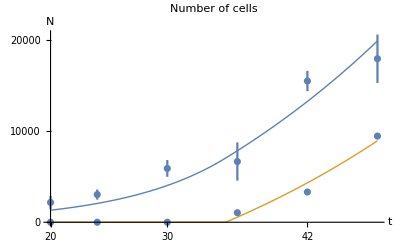

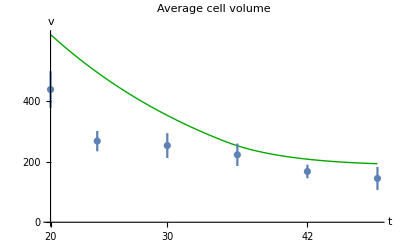

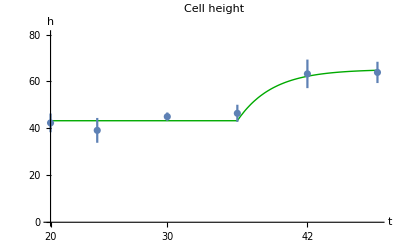

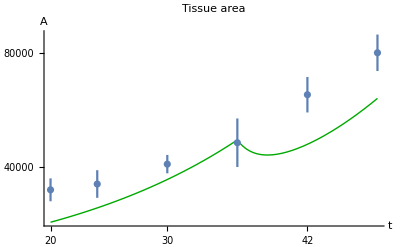

```mathematica
pfunc[t_,p_]=Piecewise[{{1,t≤35},{p,t>35}}];
heq[t_]=Piecewise[{{(h0/.solhfit),t<36},{(h1/.solhfit),t>36}}];
solalleqs[N0_,V0_,p_,g_,k_,τh_]:=NDSolve[{Np'[t]==k(pfunc[t,p]+1  pfunc[t,p]-1)Np[t],Nn'[t]==k(1- pfunc[t,p])(1+1) Np[t],Nt'[t]==k Np[t],Nt[20]== N0,Nn[20]==0,Np[20]==N0,(1/v[t])*v'[t]==g-(1/Nt[t]) Nt'[t],v[20]==V0/N0,h'[t]==-1/τh(h[t]- heq[t]),h[20]==h0/.solhfit},{Np[t],Nt[t],Nn[t],v[t],h[t]},{t,20,48}]

soltoplot=solalleqs[N0fit,V0fit,p0fit,g,kd,solτh];
solA[t_]=(Nt[t]*v[t]/h[t]*(3*(1+sexp)/(2*(1+Sqrt[sexp]+sexp))))/.soltoplot;

Show[Plot[{Nt[t]/.soltoplot,Nn[t]/.soltoplot},{t,20,48},AxesOrigin->{20,0},PlotLabel->"Number of cells",AxesStyle->Thick,LabelStyle->{FontSize->16,FontFamily->"Helvetica",Black},AxesLabel->{t,N},PlotStyle->Thick,Ticks->{{20,24,30,36,42,48},{0,10000,20000}}],ErrorListPlot[Table[{{dataNt[[i,1]],dataNt[[i,2]]},ErrorBar[datastdNt[[i,2]]]},{i,1,6}]],ErrorListPlot[Table[{{dataNn[[i,1]],dataNn[[i,2]]},ErrorBar[datastdNn[[i,2]]]},{i,1,6}]],PlotRange->All]

Show[Plot[v[t]/.soltoplot,{t,20,48},AxesOrigin->{20,0},PlotLabel->"Average cell volume",PlotStyle->{Thick,Darker[Green]},AxesStyle->Thick,LabelStyle->{FontSize->16,FontFamily->"Helvetica",Black},AxesLabel->{t,v},Ticks->{{20,24,30,36,42,48},{0,200,400}}],ErrorListPlot[Table[{{datav[[i,1]],datav[[i,2]]},ErrorBar[datastdv[[i,2]]]},{i,1,6}]]]

Show[Plot[h[t]/.soltoplot,{t,20,48},AxesOrigin->{20,0},PlotLabel->"Cell height",PlotStyle->{Thick,Darker[Green]},AxesStyle->Thick,LabelStyle->{FontSize->16,FontFamily->"Helvetica",Black},AxesLabel->{t,h},Ticks->{{20,24,30,36,42,48},{0,20,40,60,80}}],ErrorListPlot[Table[{{datah[[i,1]],datah[[i,2]]},ErrorBar[datastdh[[i,2]]]},{i,1,6}]],PlotRange->{0,80}]

Show[Plot[solA[t],{t,20,48},AxesOrigin->{20,0},PlotLabel->"Tissue area",PlotStyle->{Thick,Darker[Green]},AxesStyle->Thick,LabelStyle->{FontSize->16,FontFamily->"Helvetica",Black},AxesLabel->{t,A},Ticks->{{20,24,30,36,42,48},{0,40000,80000}}],ErrorListPlot[Table[{{dataAm[[i,1]],dataAm[[i,2]]},ErrorBar[datastdAm[[i,2]]]},{i,1,6}]],PlotRange->All]

ta=Plot[(h[t]/Sqrt[solA[t]])/.soltoplot,{t,20,48},AxesOrigin->{20,0},PlotLabel->"Tissue aspect ratio",AxesStyle->Thick,LabelStyle->{FontSize->16,FontFamily->"Helvetica",Black},AxesLabel->{t},Ticks->{{20,24,30,36,42,48},{0,0.1,0.2,0.3}}];
```

Plot experimental and theoretical decomposition of tissue volume change

```mathematica
solv[t_]=v[t]/.soltoplot;
solV[t_]=(Nt[t]*v[t])/.soltoplot;
solNt[t_]=(Nt[t])/.soltoplot;
solhsim[t_]=(h[t])/.soltoplot;
```

Decomposition of tissue volume change into cell volume change and change in number of cells
Plotted in Fig. S4D left

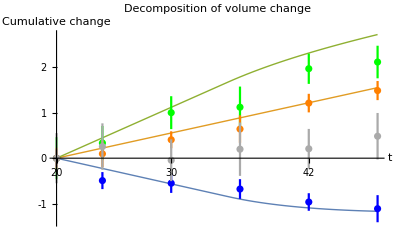

```mathematica
Show[Plot[{Log[solv[t]/solv[20]],Log[solV[t]/solV[20]],Log[solNt[t]/solNt[20]]},{t,20,48},AxesOrigin->{20,0},PlotLabel->"Decomposition of volume change",AxesStyle->Thick,LabelStyle->{FontSize->16,FontFamily->"Helvetica",Black},AxesLabel->{t,"Cumulative  change"},PlotStyle->Thick,Ticks->{{20,24,30,36,42,48},{-1,0,1,2}}],ErrorListPlot[Table[{{dataNt[[i,1]],Log[dataNt[[i,2]]/dataNt[[1,2]]]},ErrorBar[Sqrt[(datastdNt[[i,2]]/dataNt[[i,2]])^2+(datastdNt[[1,2]]/dataNt[[1,2]])^2]]},{i,1,6}],PlotStyle->Green],ErrorListPlot[Table[{{datav[[i,1]],Log[datav[[i,2]]/datav[[1,2]]]},ErrorBar[Sqrt[(datastdv[[i,2]]/datav[[i,2]])^2+(datastdv[[1,2]]/datav[[1,2]])^2]]},{i,1,6}],PlotStyle->Blue],ErrorListPlot[Table[{{dataV[[i,1]],Log[dataV[[i,2]]/dataV[[1,2]]]},ErrorBar[Sqrt[(datastdV[[i,2]]/dataV[[i,2]])^2+(datastdV[[1,2]]/dataV[[1,2]])^2]]},{i,1,6}],PlotStyle->Orange],
ErrorListPlot[Table[{{dataV[[i,1]],Log[dataV[[i,2]]/dataV[[1,2]]]-(Log[dataNt[[i,2]]/dataNt[[1,2]]]+Log[datav[[i,2]]/datav[[1,2]]])},ErrorBar[Sqrt[(datastdV[[i,2]]/dataV[[i,2]])^2+(datastdV[[1,2]]/dataV[[1,2]])^2+(datastdNt[[i,2]]/dataNt[[i,2]])^2+(datastdNt[[1,2]]/dataNt[[1,2]])^2+(datastdv[[i,2]]/datav[[i,2]])^2+(datastdv[[1,2]]/datav[[1,2]])^2]]},{i,1,6}],PlotStyle->Lighter[Gray]],PlotRange->All]
```

Decomposition of tissue volume change into area change and height change
Plotted in Fig. S4D right

The tissue surface area is calculated according to Eq. 11

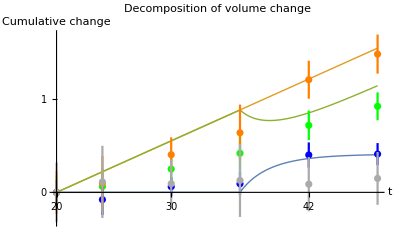

```mathematica
Show[Plot[{Log[solhsim[t]/solhsim[20]],Log[solV[t]/solV[20]],Log[solA[t]/solA[20]]},{t,20,48},AxesOrigin->{20,0},PlotLabel->"Decomposition of volume change",AxesStyle->Thick,LabelStyle->{FontSize->16,FontFamily->"Helvetica",Black},AxesLabel->{t,"Cumulative  change"},PlotStyle->Thick,Ticks->{{20,24,30,36,42,48},{-1,0,1,2}}],ErrorListPlot[Table[{{dataAm[[i,1]],Log[dataAm[[i,2]]/dataAm[[1,2]]]},ErrorBar[Sqrt[(datastdAm[[i,2]]/dataAm[[i,2]])^2+(datastdAm[[1,2]]/dataAm[[1,2]])^2]]},{i,1,6}],PlotStyle->Green],ErrorListPlot[Table[{{datah[[i,1]],Log[datah[[i,2]]/datah[[1,2]]]},ErrorBar[Sqrt[(datastdh[[i,2]]/datah[[i,2]])^2+(datastdh[[1,2]]/datah[[1,2]])^2]]},{i,1,6}],PlotStyle->Blue],
ErrorListPlot[Table[{{dataV[[i,1]],Log[dataV[[i,2]]/dataV[[1,2]]]},ErrorBar[Sqrt[(datastdV[[i,2]]/dataV[[i,2]])^2+(datastdV[[1,2]]/dataV[[1,2]])^2]]},{i,1,6}],PlotStyle->Orange],
ErrorListPlot[Table[{{dataAm[[i,1]],Log[dataV[[i,2]]/dataV[[1,2]]]-(Log[dataAm[[i,2]]/dataAm[[1,2]]]+Log[datah[[i,2]]/datah[[1,2]]])},ErrorBar[Sqrt[(datastdV[[i,2]]/dataV[[i,2]])^2+(datastdV[[1,2]]/dataV[[1,2]])^2+(datastdAm[[i,2]]/dataAm[[i,2]])^2+(datastdAm[[1,2]]/dataAm[[1,2]])^2+(datastdh[[i,2]]/datah[[i,2]])^2+(datastdh[[1,2]]/datah[[1,2]])^2]]},{i,1,6}],PlotStyle->Lighter[Gray]],PlotRange->All]
```

Combined evolution of height, volume, number of cells, with no height change

Here look at evolution of tissue aspect ratio in a situation where the tissue height is no changing.
Other parameters are taken the same as in WT.

```mathematica
pfunc[t_,p_]=Piecewise[{{1,t≤35},{p,t>35}}];
heq[t_]=h0/.solhfit;

solalleqs[N0_,V0_,p_,g_,k_,τh_]:=NDSolve[{Np'[t]==k(pfunc[t,p]+1  pfunc[t,p]-1)Np[t],Nn'[t]==k(1- pfunc[t,p])(1+1) Np[t],Nt'[t]==k Np[t],Nt[20]== N0,Nn[20]==0,Np[20]==N0,1/v[t]*v'[t]==g-1/Nt[t] Nt'[t],v[20]==V0/N0,h'[t]==-1/τh(h[t]- heq[t]),h[20]==h0/.solhfit},{Np[t],Nt[t],Nn[t],v[t],h[t]},{t,20,48}]

soltoplot=solalleqs[N0fit,V0fit,p0fit,g,kd,solτh];
solA[t_]=(Nt[t]*v[t]/h[t]*(3*(1+sexp)/(2*(1+Sqrt[sexp]+sexp))))/.soltoplot;


tanoheight=Plot[(h[t]/Sqrt[solA[t]])/.soltoplot,{t,20,48},AxesOrigin->{20,0},PlotLabel->"Tissue aspect ratio",PlotStyle->{Thick,Dashed,Red},AxesStyle->Thick,LabelStyle->{FontSize->16,FontFamily->"Helvetica",Black},AxesLabel->{t},Ticks->{{20,24,30,36,42,48},{0,0.1,0.2,0.3}}];
```

Plot simultaneously the tissue aspect ratio, with and without height change
Plotted in Fig. 6G

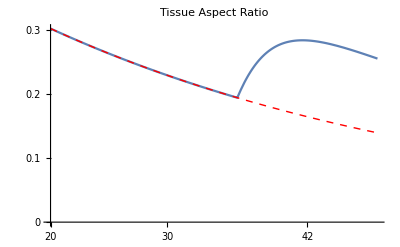

```mathematica
Show[{ta,tanoheight},PlotLabel->"Tissue Aspect Ratio",AxesStyle->Thick,LabelStyle->{FontSize->16,FontFamily->"Helvetica",Black},AxesLabel->{t},Ticks->{{20,24,30,36,42,48},{0,0.1,0.2,0.3}}]
```